## Init

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True]
ClearAll["Global`*"]
Needs["NumericalCalculus`"]
$Assumptions={_∈Reals,-Pi<θ<Pi &&-Pi<ϕ<Pi && -Pi<φ<Pi && -Pi<δ<Pi && c > 0 && ω >0 && w0>0 && z >=0 && h >0 && E0 > 0 && r >0 && l∈Reals && x∈Reals && y ∈Reals &&t>0 && β∈Reals && α∈Reals && γ∈Reals,Tp>0,T>0,a0>0,a00>0}
rule2carte ={r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
rule2pol = {x->r Cos[θ],y-> r Sin[θ]};
k := ω/c
zR:=1/2*k*w0^2 (*Rayleigh range*)
w[z] := w0 *Sqrt[1+(z/zR)^2] (* Beam radius *)
R[z] := z*(1+(zR/z)^2) (* Radius of curvature *)
p:=0
n := Abs[l]+2*p
G[z]:= (n+1)ArcTan[z/zR](* Gouy phase at z *)
Gpl := Sqrt[(2*Factorial[p])/(Pi*Factorial[p+Abs[l]])]*0+1
Lp := 1(* generalized Laguerre polynomials p = 0 -> Lp = 1 *)
If[p ==1,Lp = 1 +Abs[l]-(2*r^2)/w[z]^2;]
f[r]=(w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2];
u[r,θ,z]:=Evaluate[f[r]*Lp*Exp[-I k r^2/(2 R[z])]*Exp[-I*l*θ]*Exp[I*G[z]]];(*((2r^2)/w[z]^2)*)

Ex[r,θ,z]=E0*u[r,θ,z]*Exp[-I*k*z+I*ω*t]; (**tempEnv*)
Ey[r,θ,z]=0;
Ez[r,θ,z]=0;

Ex[x,y,z] =Ex[r,θ,z]/. {r->Norm[{x,y}],θ->ArcTan[x,y]};

Clear[l]
l=1;
c = 1;
ω = 1;
φ=0;
Ev = Evaluate[{Ex[x,y,z],0,0}]/.{Abs[x]->RealAbs[x],Abs[y]->RealAbs[y]}//Simplify
EzO3=Evaluate[-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](√2 ⅇ^(-1/2 ⅈ ((2 α^2)/(ⅈ+γ)+(2 β^2)/(ⅈ+γ)-2 (φ+t ω)-4 ArcTan[γ])) E0 (ⅈ-2 ⅈ α^2-2 α β+γ) ω)/(c h (-ⅈ+γ) (ⅈ+γ)^2)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}]; (*L=1*)
EzO5=-zR*Integrate[ⅇ^(-1/2 ⅈ h^2 γ) ,γ](-2 ⅈ √2 ⅇ^(-(ⅈ (2 α^2+2 β^2+(ⅈ+γ) (-2 (φ+t ω))))/(2 (ⅈ+γ))) E0 (-2 α^4+2 ⅈ α^3 β+2 ⅈ α β (-3+β^2+3 ⅈ γ)+α^2 (7-2 β^2-7 ⅈ γ)+(ⅈ+γ) (2 ⅈ-ⅈ β^2+2 γ)) ω)/(c h^3 (ⅈ+γ)^5)/.{α ->x/ w0, γ->z/zR,β->y/w0,h->w0}(*L=l*);
EzLGO3 = EzO3 ;
EzLGO5 = EzO3 +EzO5;
Evn2 = {Ex[x,y,z],0, EzLGO5}//Simplify;
Bn2 = I/ω *Evn2{x,y,z}//Simplify;
```

{_∈ℝ,-π<θ<π&&-π<ϕ<π&&-π<φ<π&&-π<δ<π&&c>0&&ω>0&&w0>0&&z≥0&&h>0&&E0>0&&r>0&&l∈ℝ&&x∈ℝ&&y∈ℝ&&t>0&&β∈ℝ&&α∈ℝ&&γ∈ℝ,Tp>0,T>0,a0>0,a00>0}

{(√2 ⅇ^((ⅈ t w0^2-x^2-y^2+2 t z-ⅈ w0^2 z-2 z^2+(2 ⅈ w0^2+4 z) ArcTan[(2 z)/w0^2]+(-ⅈ w0^2-2 z) ArcTan[x,y])/(w0^2-2 ⅈ z)) E0 w0^3 √(x^2+y^2))/(w0^4+4 z^2),0,0}

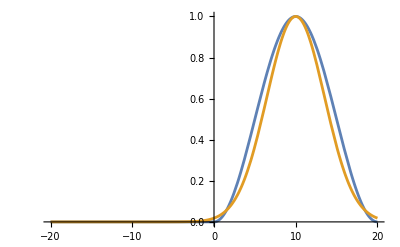

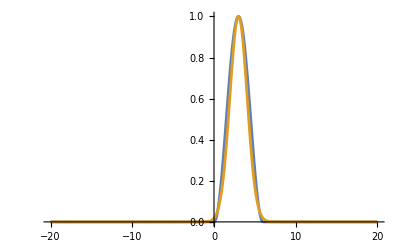

```mathematica
Plot[{Sin[Pi*t/20]^2*HeavisideTheta[t]*HeavisideTheta[1-t/20],Exp[-((t-20/2)/(20/4))^2]},{t,-20,20},PlotRange->All]
Plot[{Sin[Pi*t/6]^2*HeavisideTheta[t]*HeavisideTheta[1-t/6],Exp[-((t-6/2)/(6/4))^2]},{t,-20,20},PlotRange->All]
```

```mathematica
(*Fields with time envelope*)
```

```mathematica
sin2Env = Sin[Pi*(t-z)/T]^2*HeavisideTheta[t-z]*HeavisideTheta[1-(t-z)/T];
gaussEnv = Exp[-((t-z-T/2)/(T/4))^2];
Et=Re[Evn2]*gaussEnv/.h->w0;
Bt=Re[Bn2]*gaussEnv/.h->w0;
gam=Sqrt[1+px[t]^2+py[t]^2+pz[t]^2];
```

```mathematica
IntEzLGO5 = ComplexExpand[EzLGO5*Conjugate[EzLGO5]]*(gaussEnv)^2/.h->w0//Simplify
IntEx=((E0*w0*Gpl)/w[z]((r √2)/w[z])^Abs[l]*Exp[-r^2/w[z]^2]*gaussEnv)^2/.h->w0
```

1/((w0^4+4 z^2)^6)2 ⅇ^(-(8 (-2 t+T+2 z)^2)/T^2-(2 w0^2 x^2)/(w0^4+4 z^2)-(2 w0^2 y^2)/(w0^4+4 z^2)) E0^2 w0^6 ((w0^4+4 z^2) (w0^12-4 w0^10 x^2+4 w0^8 (4+x^4+x^2 y^2-2 x y z+3 z^2)-16 w0^6 (y^2+x^2 (7+2 z^2))+4 w0^4 (y^4+32 z^2+12 z^4-16 x y z (3+z^2)+2 x^2 y^2 (29+4 z^2)+x^4 (57+8 z^2))+16 (x^8+3 x^6 y^2-2 x^5 y z-4 x^3 y^3 z+x^4 (3 y^4+41 z^2+4 z^4)+x^2 y^2 (y^4+42 z^2+4 z^4)+z^2 (y^4+4 z^2 (4+z^2))-2 x y z (y^4+4 z^2 (6+z^2)))-16 w0^2 (7 x^6+14 x^4 y^2-8 x^3 y z-8 x y^3 z+4 y^2 z^2+x^2 (7 y^4+4 z^2 (7+z^2))))+4 (2 w0^14-w0^12 (11 x^2+y^2)+8 w0^10 (2 x^4+2 x^2 y^2-4 x y z-z^2)-128 w0^2 z^4 (4 x^4+4 x^2 y^2-8 x y z+3 z^2)-32 w0^6 z^2 (6 x^4+6 x^2 y^2-4 x y z+5 z^2)-4 w0^8 (x^6+2 x^4 y^2-2 x^3 y z-2 x y^3 z-5 y^2 z^2+x^2 (y^4-31 z^2))-64 z^4 (x^6+2 x^4 y^2-2 x^3 y z-2 x y^3 z+y^2 z^2+x^2 (y^4+3 z^2))+16 w0^4 z^2 (6 x^6+12 x^4 y^2-12 x^3 y z-12 x y^3 z+5 y^2 z^2+x^2 (6 y^4+39 z^2))) Cos[Arg[1-(2 ⅈ z)/w0^2]-Arg[1+(2 ⅈ z)/w0^2]]-8 (-4 w0^10 (9 x^2+y^2) z+w0^12 (x y+6 z)+16 w0^4 z^3 (2 x^4+2 x^2 y^2-13 x y z+2 z^2)-64 z^5 (3 x^4+3 x^2 y^2-5 x y z+2 z^2)+4 w0^8 z (13 x^4+13 x^2 y^2-17 x y z+10 z^2)-16 w0^6 x z (x^5+2 x^3 y^2-2 x^2 y z-2 y^3 z+x (y^4+4 z^2))+64 w0^2 z^3 (x^6+2 x^4 y^2-2 x^3 y z-2 x y^3 z+y^2 z^2+x^2 (y^4+5 z^2))) Sin[Arg[1-(2 ⅈ z)/w0^2]-Arg[1+(2 ⅈ z)/w0^2]])

(2 ⅇ^(-(32 (t-T/2-z)^2)/T^2-(2 r^2)/(w0^2 (1+(4 z^2)/w0^4))) E0^2 r^2)/(w0^2 (1+(4 z^2)/w0^4)^2)

```mathematica
FponderoEx = -1/4*Grad[IntEx/.{r->Sqrt[x^2+y^2]},{x,y,z}]//Simplify
```

{-(ⅇ^(-(8 (-2 t+T+2 z)^2)/T^2-(2 w0^2 x^2)/(w0^4+4 z^2)-(2 w0^2 y^2)/(w0^4+4 z^2)) E0^2 w0^6 x (w0^4-2 w0^2 (x^2+y^2)+4 z^2))/((w0^4+4 z^2)^3),-(ⅇ^(-(8 (-2 t+T+2 z)^2)/T^2-(2 w0^2 x^2)/(w0^4+4 z^2)-(2 w0^2 y^2)/(w0^4+4 z^2)) E0^2 w0^6 y (w0^4-2 w0^2 (x^2+y^2)+4 z^2))/((w0^4+4 z^2)^3),(8 ⅇ^(-(8 (-2 t+T+2 z)^2)/T^2-(2 w0^2 x^2)/(w0^4+4 z^2)-(2 w0^2 y^2)/(w0^4+4 z^2)) E0^2 w0^6 (x^2+y^2) (-4 t (w0^4+4 z^2)^2+2 T (w0^4+4 z^2)^2+4 z (w0^4+4 z^2)^2+T^2 z (w0^4-w0^2 (x^2+y^2)+4 z^2)))/(T^2 (w0^4+4 z^2)^4)}

```mathematica
(**)
```

```mathematica
FponderoEz={1/((w0^4+4 z^2)^6)2 ⅇ^(-8+(32 (t-z) (-t+T+z))/T^2-(2 w0^2 (x^2+y^2))/(w0^4+4 z^2)) E0^2 w0^6 (3 w0^14 x+w0^12 (-2 x (-15+4 x^2+y^2)+2 y z)+4 w0^8 (22 x^5+x y^2 (-33+2 y^2)+x^3 (-85+24 y^2)-2 y (-6+15 x^2+y^2) z-2 x (10 x^2+3 (-9+y^2)) z^2+6 y z^3)+4 w0^6 (-x (x^2+y^2) (4 x^4-15 y^2+x^2 (-99+4 y^2))+8 y (x^4-y^2+x^2 (-9+y^2)) z+8 x (18-16 x^2+x^4+(-6+x^2) y^2) z^2-16 (-3+x^2) y z^3+36 x z^4)+32 z^2 (-x (x^2+y^2)^2 (4 x^2+y^2)+y (x^2+y^2) (5 x^2+y^2) z-2 x (6 x^4+21 y^2+2 y^4+x^2 (41+8 y^2)) z^2+4 y (6+3 x^2+y^2) z^3-4 x (3+2 x^2+y^2) z^4+4 y z^5)+8 w0^4 (-x (x^2+y^2)^2 (18 x^2+y^2)+y (x^2+y^2) (21 x^2+y^2) z+4 x (4 x^4-27 y^2+x^2 (-63+4 y^2)) z^2-48 (-1+x^2) y z^3-4 x (-9+8 x^2+3 y^2) z^4+12 y z^5)+16 w0^2 (x^3 (x^2+y^2)^3-2 x^2 y (x^2+y^2)^2 z+x (x^2+y^2) (4 x^4+15 y^2+x^2 (83+4 y^2)) z^2-8 y (x^4+y^2+x^2 (9+y^2)) z^3+4 x (18-5 x^2+x^4+(-3+x^2) y^2) z^4-8 (-3+x^2) y z^5+12 x z^6)+4 w0^10 (x^5+x^3 (-27+y^2)+6 y z-2 x^2 y z+9 x (2-y^2+z^2))),1/((w0^4+4 z^2)^6)2 ⅇ^(-8+(32 (t-z) (-t+T+z))/T^2-(2 w0^2 (x^2+y^2))/(w0^4+4 z^2)) E0^2 w0^6 (w0^14 y+2 w0^12 ((5-3 x^2) y+x z)+4 w0^6 (-y (x^2+y^2) (4 x^4-y^2+x^2 (-85+4 y^2))+8 x (-9 y^2+y^4+x^2 (-1+y^2)) z+8 y (6+x^4+x^2 (-10+y^2)) z^2-16 x (-3+y^2) z^3+12 y z^4)+32 z^2 (-3 x^2 y (x^2+y^2)^2+x (x^2+y^2) (x^2+5 y^2) z-2 y (4 x^4+y^2+x^2 (21+4 y^2)) z^2+4 x (6+x^2+3 y^2) z^3-4 (1+x^2) y z^4+4 x z^5)+8 w0^4 (-17 x^2 y (x^2+y^2)^2+x (x^2+y^2) (x^2+21 y^2) z+4 y (4 x^4-3 y^2+x^2 (-39+4 y^2)) z^2-48 x (-1+y^2) z^3+4 (3-5 x^2) y z^4+12 x z^5)+16 w0^2 (x^2 y (x^2+y^2)^3-2 x y^2 (x^2+y^2)^2 z+y (x^2+y^2) (4 x^4+y^2+x^2 (69+4 y^2)) z^2-8 x (x^2+(9+x^2) y^2+y^4) z^3+4 y (6+x^4+y^2+x^2 (-1+y^2)) z^4-8 x (-3+y^2) z^5+4 y z^6)+4 w0^8 (20 x^4 y-5 y^3-2 x^3 z+18 y z^2+x^2 y (-57+20 y^2-14 z^2)+6 x z (2-5 y^2+z^2))+4 w0^10 ((-1+x^2) y^3+6 x z-2 x y^2 z+y (6-19 x^2+x^4+3 z^2))),1/((w0^4+4 z^2)^6)4 ⅇ^(-8+(32 (t-z) (-t+T+z))/T^2-(2 w0^2 (x^2+y^2))/(w0^4+4 z^2)) E0^2 w0^6 (w0^4 x y (16 w0^6+w0^8-4 w0^4 (-6+x^2+y^2)-16 w0^2 (x^2+y^2)+4 (x^2+y^2)^2)-4 (w0^12+w0^10 (4-3 x^2)-28 w0^2 x^2 (x^2+y^2)^2+4 x^2 (x^2+y^2)^3+4 w0^6 (x^4-2 y^2+x^2 (-14+y^2))+w0^8 (12+3 x^4+y^2+x^2 (-5+3 y^2))+2 w0^4 (x^2+y^2) (4 x^4+y^2+x^2 (49+4 y^2))) z+4 x y (56 w0^6+9 w0^8-48 w0^2 (x^2+y^2)+12 (x^2+y^2)^2+16 w0^4 (9+x^2+y^2)) z^2-16 (3 w0^8+w0^6 (8-6 x^2)+4 w0^2 (x^4-2 y^2+x^2 (-14+y^2))+2 (x^2+y^2) (4 x^4+y^2+x^2 (41+4 y^2))+w0^4 (6 x^4+4 (6+y^2)+x^2 (4+6 y^2))) z^3+80 x y (8 w0^2+3 w0^4+4 (6+x^2+y^2)) z^4-64 (3 w0^4+w0^2 (4-3 x^2)+3 (4+x^4+y^2+x^2 (3+y^2))) z^5+448 x y z^6-256 z^7+6 z (w0^12-4 w0^10 (-2+x^2)+4 w0^8 (4+x^4-y^2+x^2 (-11+y^2)-2 x y z+3 z^2)+16 w0^2 (-7 x^2 (x^2+y^2)^2+8 x y (x^2+y^2) z+4 (2 x^4-y^2+x^2 (-7+2 y^2)) z^2-24 x y z^3-4 (-2+x^2) z^4)+16 (x^2 (x^2+y^2)^3-2 x y (x^2+y^2)^2 z+(x^2+y^2) (4 x^4+y^2+x^2 (41+4 y^2)) z^2-8 x y (6+x^2+y^2) z^3+4 (4+x^4+y^2+x^2 (3+y^2)) z^4-8 x y z^5+4 z^6)+16 w0^6 (4 x^4-y^2-6 x y z+4 z^2+x^2 (-7+4 y^2-2 z^2))+4 w0^4 (-4 x^6+y^4+8 x^3 y z+32 z^2+12 z^4+8 x y z (-6+y^2-2 z^2)+x^4 (57-8 y^2+8 z^2)+x^2 (58 y^2-4 y^4+8 (-4+y^2) z^2)))-2 (w0^4+4 z^2) ((4 t)/T^2-2/T-(4 z)/T^2+(w0^2 (x^2+y^2) z)/((w0^4+4 z^2)^2)) (w0^12-4 w0^10 (-2+x^2)+4 w0^8 (4+x^4-y^2+x^2 (-11+y^2)-2 x y z+3 z^2)+16 w0^2 (-7 x^2 (x^2+y^2)^2+8 x y (x^2+y^2) z+4 (2 x^4-y^2+x^2 (-7+2 y^2)) z^2-24 x y z^3-4 (-2+x^2) z^4)+16 (x^2 (x^2+y^2)^3-2 x y (x^2+y^2)^2 z+(x^2+y^2) (4 x^4+y^2+x^2 (41+4 y^2)) z^2-8 x y (6+x^2+y^2) z^3+4 (4+x^4+y^2+x^2 (3+y^2)) z^4-8 x y z^5+4 z^6)+16 w0^6 (4 x^4-y^2-6 x y z+4 z^2+x^2 (-7+4 y^2-2 z^2))+4 w0^4 (-4 x^6+y^4+8 x^3 y z+32 z^2+12 z^4+8 x y z (-6+y^2-2 z^2)+x^4 (57-8 y^2+8 z^2)+x^2 (58 y^2-4 y^4+8 (-4+y^2) z^2)))-1/w0^2 2 ⅈ (w0^4+4 z^2) (-2 w0^6 (7 x^2+y^2) z+w0^8 (x y+2 z)+16 z^3 (3 x^2 (x^2+y^2)-5 x y z+2 z^2)+4 w0^4 z (5 x^2 (x^2+y^2)-4 x y z+4 z^2)-8 w0^2 z (x^2 (x^2+y^2)^2-2 x y (x^2+y^2) z+(7 x^2+y^2) z^2)) (Arg'[1-(2 ⅈ z)/w0^2]+Arg'[1+(2 ⅈ z)/w0^2]))};
```

```mathematica
(*Equation of motion*)
```

```mathematica
eq0={D[px[t],t],D[py[t],t],D[pz[t],t]}-ee*(Et+Cross[{px[t],py[t],pz[t]},Bt]/gam)/.{x->x[t],y->y[t],z->z[t]};
Fpondero = FponderoEx+FponderoEz//Simplify;
eq0Pondero={D[px[t],t],D[py[t],t],D[pz[t],t]}-Fpondero/.{x->x[t],y->y[t],z->z[t]};
eq0PonderoRelat={D[px[t],t],D[py[t],t],D[pz[t],t]}-Fpondero/gam/.{x->x[t],y->y[t],z->z[t]};
```

```mathematica
(*Function, which solves equation of motion*)
```

```mathematica
sol[a00_,w00_,T0_,x0_,y0_,z0_,dt_,tmax_,ee0_]:=NDSolve[{(eq0=={0,0,0})/.{E0->a00,T->T0,w0->w00,ee->ee0},D[y[t],t]==py[t]/gam,D[z[t],t]==pz[t]/gam,D[x[t],t]==px[t]/gam,px[-20]==0,py[-20]==0,pz[-20]==0,x[-20]==x0,y[-20]==y0,z[-20]==z0},{px,py,pz,x,y,z},{t,-20,tmax},StartingStepSize->dt,PrecisionGoal->20]
solPondero[a00_,w00_,T0_,x0_,y0_,z0_,dt_,tmax_,ee0_]:=NDSolve[{(eq0Pondero=={0,0,0})/.{E0->a00,T->T0,w0->w00,ee->ee0},D[y[t],t]==py[t]/gam,D[z[t],t]==pz[t]/gam,D[x[t],t]==px[t]/gam,px[-20]==0,py[-20]==0,pz[-20]==0,x[-20]==x0,y[-20]==y0,z[-20]==z0},{px,py,pz,x,y,z},{t,-20,tmax},StartingStepSize->dt,PrecisionGoal->20]
solPonderoRelat[a00_,w00_,T0_,x0_,y0_,z0_,dt_,tmax_,ee0_]:=NDSolve[{(eq0PonderoRelat=={0,0,0})/.{E0->a00,T->T0,w0->w00,ee->ee0},D[y[t],t]==py[t]/gam,D[z[t],t]==pz[t]/gam,D[x[t],t]==px[t]/gam,px[-20]==0,py[-20]==0,pz[-20]==0,x[-20]==x0,y[-20]==y0,z[-20]==z0},{px,py,pz,x,y,z},{t,-20,tmax},StartingStepSize->dt,PrecisionGoal->20]
```

```mathematica
(*Calculation of Mz for 4 particles starting at (1,1), (-1,1), (-1,-1) and (1,-1)*)
```

```mathematica
MzDistrib[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,mz},
soll=sol[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax]

PrDistribPondero[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,pr},
soll=solPondero[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];pr =((x[t]*px[t]+y[t]*py[t])/Sqrt[x[t]^2+y[t]^2]/.soll)/.t->tmax](*mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax*)
PrDistrib[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,pr},
soll=sol[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];pr=((x[t]*px[t]+y[t]*py[t])/Sqrt[x[t]^2+y[t]^2]/.soll)/.t->tmax](*mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax*)

MzDistribPondero[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,mz},
soll=solPondero[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];
mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax]
MzDistribPonderoRelat[x0_,y0_,z0_, a00_,w00_,T0_,dt_,tmax_,ee0_]:=Module[{soll,mz},
soll=solPonderoRelat[a00,w00,T0,x0,y0,z0,dt,tmax,ee0];
mz=(x[t]*py[t]-y[t]*px[t]/.soll)/.t->tmax]
```

```mathematica
f[r]^2/.{z->0}
derivative =D[f[r]^2,r]/.{z->0}//FullSimplify
(*FullSimplify[(4 ⅇ^(-(2 r^2)/(w0^2 (1+(4 z^2)/w0^4))) r^2)/(w0^2 (1+(4 z^2)/w0^4)^2(1+(4 z^2)/w0^4))*(Abs[l]-(2 r^2)/w0^2+(4 z^2)/w0^4)*1/r]===FullSimplify[derivative]
FullSimplify[(4 ⅇ^(-(2 r^2)/(w0^2 (1+(4 z^2)/w0^4))) r^2)/w0^2*(Abs[l]-(2 r^2)/w0^2)*1/r]===FullSimplify[derivative]
FullSimplify[(2w0)/w[z]^2*f[r]^2*(Abs[l]-(2 r^2)/w0^2+(4 z^2)/w0^4)*w0/r]===FullSimplify[derivative]*)
FullSimplify[2*(f[r]^2)(Abs[l]-(2 r^2)/w0^2)*1/r]===Simplify[derivative]
```

(2 ⅇ^(-(2 r^2)/w0^2) r^2)/w0^2

(4 ⅇ^(-(2 r^2)/w0^2) r (-2 r^2+w0^2))/w0^4

False

### Lz Model

```mathematica
IntEzLGO5polar=IntEzLGO5/.rule2pol//Simplify
```

1/((w0^4+4 z^2)^6)2 ⅇ^(-(8 (-2 t+T+2 z)^2)/T^2-(2 r^2 w0^2 Cos[θ]^2)/(w0^4+4 z^2)-(2 r^2 w0^2 Sin[θ]^2)/(w0^4+4 z^2)) E0^2 w0^6 ((w0^4+4 z^2) (w0^12-4 r^2 w0^10 Cos[θ]^2-16 r^2 w0^6 (4+z^2+(3+z^2) Cos[2 θ])-8 r^2 w0^2 (7 r^4+32 z^2+4 z^4+(7 r^4+4 z^2 (6+z^2)) Cos[2 θ]-8 r^2 z Sin[2 θ])+2 w0^8 (8+r^4+6 z^2+r^4 Cos[2 θ]-2 r^2 z Sin[2 θ])+4 w0^4 (29 r^4+32 z^2+4 r^4 z^2+12 z^4+4 r^4 (7+z^2) Cos[2 θ]-8 r^2 z (3+z^2) Sin[2 θ])+8 (r^8+42 r^4 z^2+32 z^4+4 r^4 z^4+8 z^6+r^4 (r^4+4 z^2 (10+z^2)) Cos[2 θ]-2 r^2 z (r^4+4 z^2 (6+z^2)) Sin[2 θ]))-4 Cos[Arg[1-(2 ⅈ z)/w0^2]-Arg[1+(2 ⅈ z)/w0^2]] (r^2 (5 w0^12-52 w0^8 z^2-272 w0^4 z^4+64 z^6-8 r^2 w0^2 (w0^8-12 w0^4 z^2-32 z^4)+2 r^4 (w0^8-24 w0^4 z^2+16 z^4)) Cos[2 θ]+2 (-((w0^4-12 z^2) (w0^5+4 w0 z^2)^2)-4 r^4 w0^2 (w0^8-12 w0^4 z^2-32 z^4)+r^6 (w0^8-24 w0^4 z^2+16 z^4)+r^2 (3 w0^12-36 w0^8 z^2-176 w0^4 z^4+64 z^6)-2 r^2 z (-4 w0^2 (w0^8-4 w0^4 z^2-32 z^4)+r^2 (w0^8-24 w0^4 z^2+16 z^4)) Sin[2 θ]))-4 (-4 z (-((3 w0^4-4 z^2) (w0^4+4 z^2)^2)+4 r^6 (w0^6-4 w0^2 z^2)+2 r^2 w0^2 (5 w0^8+8 w0^4 z^2-48 z^4)+r^4 (-13 w0^8-8 w0^4 z^2+48 z^4))+4 r^2 z (-4 r^4 (w0^6-4 w0^2 z^2)+r^2 (13 w0^8+8 w0^4 z^2-48 z^4)-8 w0^2 (w0^8+2 w0^4 z^2-8 z^4)) Cos[2 θ]+r^2 (w0^12+32 r^2 w0^6 z^2-68 w0^8 z^2-128 r^2 w0^2 z^4-208 w0^4 z^4+320 z^6) Sin[2 θ]) Sin[Arg[1-(2 ⅈ z)/w0^2]-Arg[1+(2 ⅈ z)/w0^2]])

```mathematica
Fθ[r_,θ_,z_,t_] = -1/4*1/r*D[IntEzLGO5polar,θ]//Simplify;
Lz2[r_,θ_,z_,a0_,w0_,Tp_] = r*Integrate[Fθ[r,θ,z,t]/.{E0->a0,T->Tp},{t,0,Tp}]//FullSimplify
```

-1/(4 (w0^4+4 z^2)^5)a0^2 ⅇ^(-(2 r^2 w0^2)/(w0^4+4 z^2)) √(π/2) r^2 Tp w0^6 (Erf[(2 √2 (Tp+2 z))/Tp]+Erf[(2 √2 (Tp-2 z))/Tp] Sign[Tp-2 z]) (-2 z (4 r^4-4 r^2 (4 w0^2+w0^4-4 z^2)+(w0^4+4 z^2) (24+12 w0^2+w0^4+4 z^2)) Cos[2 θ]+(-4 r^6+4 r^4 (7 w0^2+w0^4-4 z^2)+(w0^4+4 z^2) (w0^2 (4+w0^2) (6+w0^2)+4 (-2+w0^2) z^2)-r^2 (w0^4 (56+16 w0^2+w0^4)+8 (20+4 w0^2+w0^4) z^2+16 z^4)) Sin[2 θ])

## Numerical

```mathematica
l0=2Pi;
tmax = 50*l0;
dt = 0.000001;
w0=2.5*l0;
a0=2.0;
z0=5*l0;
Tp=12*l0;
```

### Radial momentum Pr

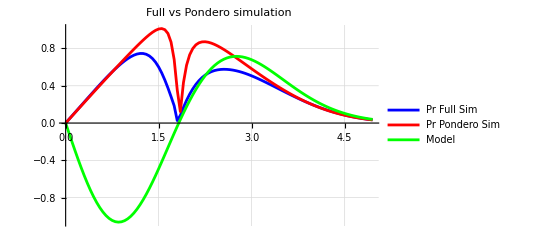

```mathematica
dxTable = 0.05;
PrTable = ParallelTable[{Max[Table[PrDistrib[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,a0,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
PrPonderoTable = ParallelTable[{Max[Table[PrDistribPondero[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,a0,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];

PrModelTable = ParallelTable[{(-a0^2/4*D[f[r]^2,r]*3/8*Tp)/.{z->z0,r->r0*l0}},{r0,0.0001,2*w0/l0,dxTable}];

td=TemporalData[{PrTable,PrPonderoTable,PrModelTable},{0.0001,2*w0/l0,dxTable}];
ListLinePlot[td,PlotStyle->{Blue,Red,Green},GridLines->Automatic,PlotLabel->"Full vs Pondero simulation",PlotLegends->Placed[{"Pr Full Sim","Pr Pondero Sim","Model"},Right]]
```

12.5655

0.2+0.128794 Erf[(-22 π+t)/(3 √2 π)]

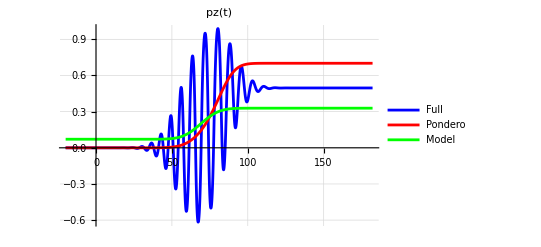

```mathematica
x0Traj=-1.37479*l0;
y0Traj=-1.452379*l0;
z0Traj = 5*l0;
r0Traj = Sqrt[x0Traj^2+y0Traj^2]
FponderoR=-a0^2/4 D[f[r]^2,r]*gaussEnv^2/.{T->Tp,z->z0Traj,r->r0Traj};
(*FponderoZgrad =(-1/4*D[IntEx,z]//Simplify)/.{T->Tp,E0->a0,r->1.5*l0,z->0}//Simplify;*)
prModel[t_] = Integrate[FponderoR,t]+0.2
sollPondero=solPondero[a0,w0,Tp,x0Traj,y0Traj,z0Traj,dt,Tp*2+z0Traj,-1];
prSolPondero[t_]=((x[t]*px[t]+y[t]*py[t])/Sqrt[x[t]^2+y[t]^2]/.sollPondero);
soll=sol[a0,w0,Tp,x0Traj,y0Traj,z0Traj,dt,Tp*2+z0Traj,-1];
prSol[t_]=((x[t]*px[t]+y[t]*py[t])/Sqrt[x[t]^2+y[t]^2]/.soll);
Plot[{prSol[t],prSolPondero[t],prModel[t]},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"Full","Pondero","Model"},PlotLabel->"pz(t)"]
```

### Longitudinal Momentum & Displacement

```mathematica
x0Traj=2*l0;
y0Traj=2*l0;
z0Traj = 5*l0;
r0Traj = Sqrt[x0Traj^2+y0Traj^2]
```

4 √2 π

```mathematica
FponderoZ =-a0^2/4 f[r]^2*D[gaussEnv^2,z]/.{T->Tp,z->z0Traj,r->r0Traj};
(*FponderoZgrad =(-1/4*D[IntEx,z]//Simplify)/.{T->Tp,E0->a0,r->1.5*l0,z->0}//Simplify;*)
pzModel[t_] = Integrate[FponderoZ,t]
zModel[t_]=Integrate[Integrate[FponderoZ,{t,0,t}],{t,0,t}]+z0Traj
```

0.203975 ⅇ^(-0.0225158 (50.2655-1. t)^2)-5.89859×10^-16 Erf[0.150053 (50.2655-1. t)]

32.6206-4.44089×10^-16 t-1.2047 Erf[7.54247-0.150053 t]

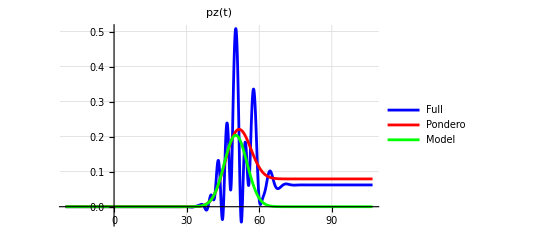

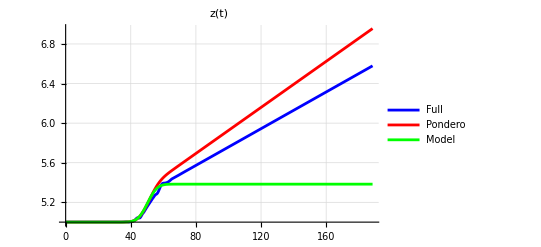

```mathematica
sollPondero=solPondero[a0,w0,Tp,x0Traj,y0Traj,z0Traj,dt,Tp*2+z0Traj,-1];
pzSolPondero[t_]=(pz[t]/.sollPondero);
zSolPondero[t_]=(z[t]/.sollPondero);
soll=sol[a0,w0,Tp,x0Traj,y0Traj,z0Traj,dt,Tp*2+z0Traj,-1];
pzSol[t_]=(pz[t]/.soll);
zSol[t_]=(z[t]/.soll);
Plot[{pzSol[t],pzSolPondero[t],pzModel[t]},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"Full","Pondero","Model"},PlotLabel->"pz(t)"]
Plot[{zSol[t]/l0,zSolPondero[t]/l0,zModel[t]/l0},{t,0,30*l0},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"Full","Pondero","Model"},PlotLabel->"z(t)"]
```

### Particle Trajector

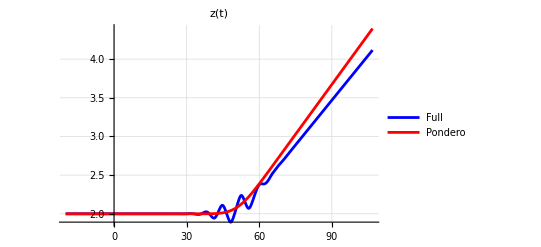

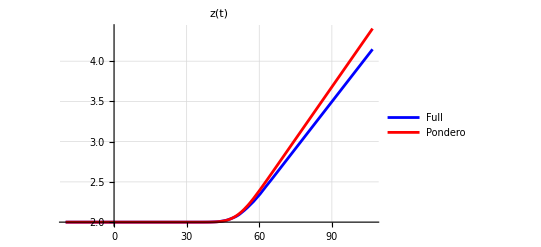

```mathematica
xSolPondero[t_]=(x[t]/.sollPondero);
ySolPondero[t_]=(y[t]/.sollPondero);
pxSolPondero[t_]=(px[t]/.soll);
pySolPondero[t_]=(py[t]/.soll);
xSol[t_]=(x[t]/.soll);
ySol[t_]=(y[t]/.soll);
pxSol[t_]=(px[t]/.soll);
pySol[t_]=(py[t]/.soll);

Plot[{xSol[t]/l0,xSolPondero[t]/l0},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"Full","Pondero"},PlotLabel->"z(t)"]
Plot[{ySol[t]/l0,ySolPondero[t]/l0},{t,-20,Tp*2+z0Traj},PlotRange->All,GridLines->Automatic,PlotStyle->{Blue,Red,Green},PlotLegends->{"Full","Pondero"},PlotLabel->"z(t)"]
```

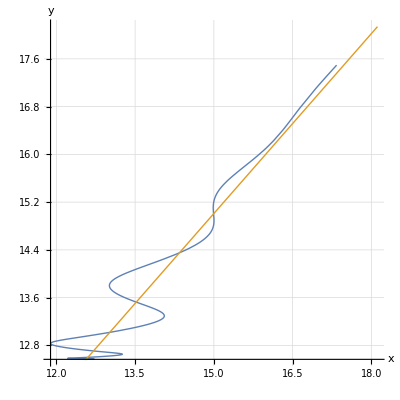

```mathematica
ParametricPlot[{{xSol[t][[1]],ySol[t][[1]]},{xSolPondero[t][[1]],ySolPondero[t][[1]]},{x0Traj+t*0.0003,y0Traj+t*0.0003}},{t,0,Tp*1.9},PlotStyle->Thick,AxesLabel->{"x","y"},AspectRatio->1,PlotRange->Full,GridLines->Automatic]
```

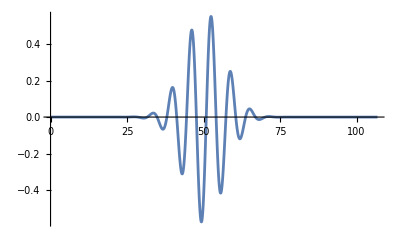

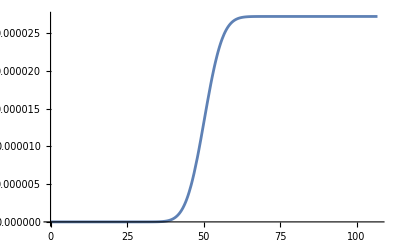

```mathematica
LzSol[t_] = ((x[t]*py[t]-y[t]*px[t])/.{soll});
LzSolPondero[t_] =((x[t]*py[t]-y[t]*px[t])/.{sollPondero});
Plot[{LzSol[t] },{t,0,Tp*2+z0Traj},PlotRange->All]
Plot[{LzSolPondero[t]},{t,0,Tp*2+z0Traj},PlotRange->All]
```

### Angular Momentum Lz

```mathematica
MzDistrib[1,2,z0,10^p,w0,Tp,dt,tmax,-1]
MzDistribPondero[1,2,z0,10^p,w0,Tp,dt,tmax,-1]
MzDistribPonderoRelat[1,2,z0,10^p,w0,Tp,dt,tmax,-1]
```

{0.0011931}

{-0.00125104}

{-0.00124989}

#### Scaling with a0

```mathematica
pda0 = 0.05;
a0ScalingListPondero = ParallelTable[{10^p,Max[Table[Max[Table[MzDistribPondero[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,10^p,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]],{r0,0.0001,2*w0/l0,0.25}]]},{p,-0.75,0.5,pda0}];
a0ScalingListPonderoRelat = ParallelTable[{10^p,Max[Table[Max[Table[MzDistribPonderoRelat[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,10^p,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]],{r0,0.0001,2*w0/l0,0.25}]]},{p,-0.75,0.5,pda0}];
a0ScalingListModel = Table[{10^p,Max[Table[Max[Table[Lz2[r0*l0,theta,z0,10^p,w0,Tp],{theta,0,2Pi,Pi/8}]],{r0,0.0001,2*w0/l0,0.1}]]},{p,-0.75,0.5,pda0}];
a0ScalingListModelGamma = Table[{10^p,Sqrt[1+(10^p)^2]*Max[Table[Max[Table[Lz2[r0*l0,theta,z0,10^p,w0,Tp],{theta,0,2Pi,Pi/8}]],{r0,0.0001,2*w0/l0,0.1}]]},{p,-0.75,0.5,pda0}];
```

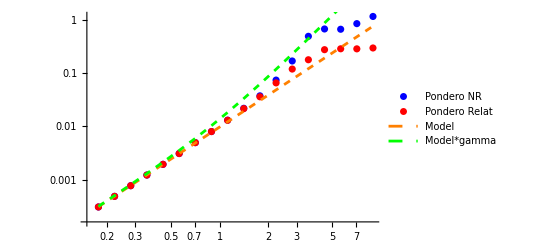

```mathematica
Show[ListLogLogPlot[a0ScalingListPondero,PlotStyle->Blue,Joined->False,GridLines->Automatic,PlotLegends->{"Pondero NR"}],ListLogLogPlot[a0ScalingListPonderoRelat,PlotStyle->Red,Joined->False,GridLines->Automatic,PlotLegends->{"Pondero Relat"}],ListLogLogPlot[a0ScalingListModel,PlotStyle->{Orange,Dashed},Joined->True,GridLines->Automatic,PlotLegends->{"Model"}],ListLogLogPlot[a0ScalingListModelGamma,PlotStyle->{Green,Dashed},Joined->True,GridLines->Automatic,PlotLegends->{"Model*gamma"}]]
(*Show[ListLogLogPlot[data[[All,{1,2}]],PlotStyle->Red],ListLogLogPlot[data[[All,{1,3}]],PlotStyle->Blue]]*)
```

#### Radial distribution

```mathematica
a0=2.0;
Tp=6*l0;
w0=2.5*l0
dxTable = 0.1;
MzTable = ParallelTable[{Max[Table[MzDistrib[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,a0,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzPonderoTable = ParallelTable[{Max[Table[MzDistribPondero[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,a0,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzPonderoRelatTable = ParallelTable[{Max[Table[MzDistribPonderoRelat[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,a0,w0,Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzModelTable = ParallelTable[{Max[Table[Lz2[r0*l0,theta,z0,a0,w0,Tp],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
```

15.708

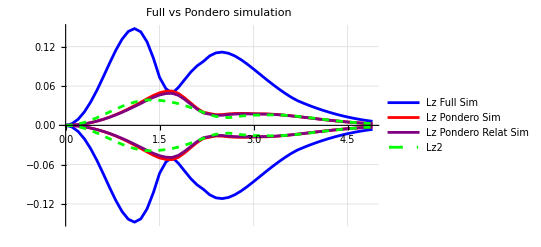

```mathematica
td=TemporalData[{MzTable,-MzTable,MzPonderoTable,-MzPonderoTable,MzPonderoRelatTable,-MzPonderoRelatTable,MzModelTable,-MzModelTable},{0.0001,2*w0/l0,dxTable}];
ListLinePlot[td,PlotStyle->{Blue,Blue,Red,Red,Purple,Purple,{Green,Dashed},{Green,Dashed}},GridLines->Automatic,PlotLabel->"Full vs Pondero simulation",PlotLegends->Placed[{"Lz Full Sim",None,"Lz Pondero Sim",None,"Lz Pondero Relat Sim",None,"Lz2",None},Right]]
```

```mathematica
Table[{Max[Table[Lz2[r0*l0,theta,z0,a0,w0,6*l0],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}]
Table[{Max[Table[Lz2[r0*l0,theta,z0,a0,w0,120*l0],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}]
```

{{1.31185×10^-12},{5.15589×10^-6},{0.0000194906},{0.0000399041},{0.0000620461},{0.0000813056},{0.0000938073},{0.0000971692},{0.0000923356},{0.0000827591},{0.0000676214},{0.0000493944},{0.0000339344},{0.0000294264},{0.0000353442},{0.0000388137},{0.0000394786},{0.0000396551},{0.0000367039},{0.0000318512},{0.0000261778},{0.0000205093},{0.0000153855},{0.0000110868},{7.69258×10^-6}}

{{2.63345×10^-11},{0.000103501},{0.000391259},{0.000801047},{0.00124553},{0.00163215},{0.00188312},{0.0019506},{0.00185357},{0.00166133},{0.00135745},{0.000991556},{0.000681209},{0.000590715},{0.000709509},{0.000779158},{0.000792505},{0.000796048},{0.000736805},{0.00063939},{0.0005255},{0.00041171},{0.000308853},{0.000222559},{0.000154423}}

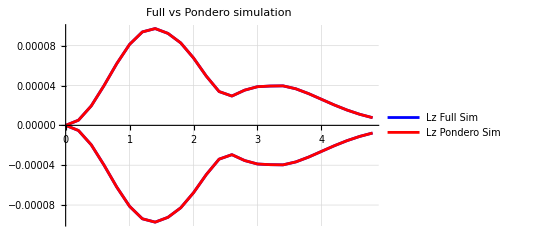

```mathematica
dxTable = 0.2;
MzModelTable1 = ParallelTable[{Max[Table[Lz2[r0*l0,theta,z0,a0,w0,6*l0],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzModelTable2 = ParallelTable[{Max[Table[Lz2[r0*l0,theta,z0,a0,w0,120*l0],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
td=TemporalData[{MzModelTable1,-MzModelTable1,MzModelTable2,-MzModelTable2},{0.0001,2*w0/l0,dxTable}];
ListLinePlot[td,PlotStyle->{Blue,Blue,Red,Red},GridLines->Automatic,PlotLabel->"Full vs Pondero simulation",PlotLegends->Placed[{"Lz Full Sim",None,"Lz Pondero Sim"},Right]]
```

0.1

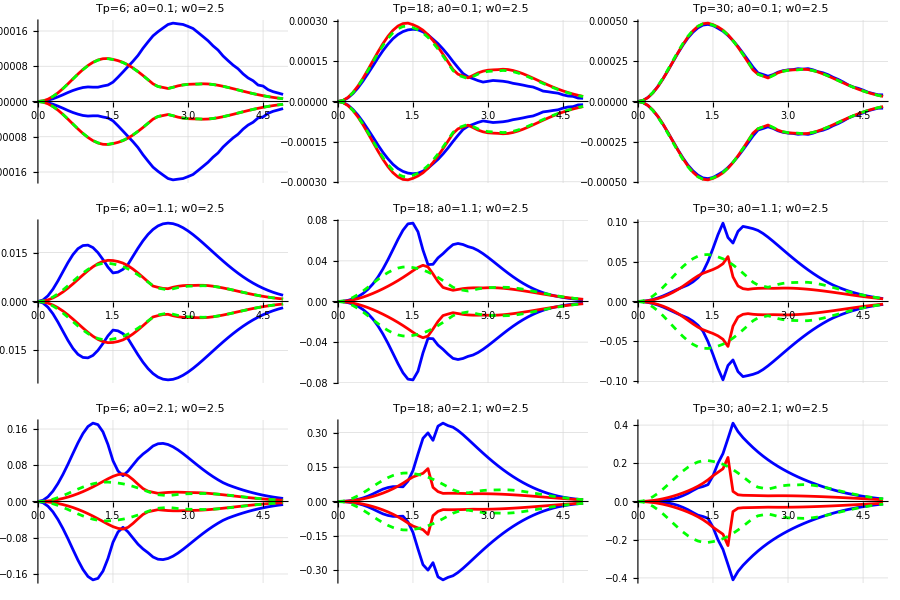

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]

dxTable = 0.1;
a0=0.1
pt=Table[MzTable = ParallelTable[{Max[Table[MzDistrib[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,n+a0,w0,m*Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzPonderoTable = ParallelTable[{Max[Table[MzDistribPondero[r0*l0*Cos[theta],r0*l0*Sin[theta],z0,n+a0,w0,m*Tp,dt,tmax,-1],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
MzModelTable=Table[{Max[Table[Lz2[r0*l0,theta,z0,n+a0,w0,m*Tp],{theta,0,2Pi,Pi/8}]]},{r0,0.0001,2*w0/l0,dxTable}];
td=TemporalData[{MzTable,-MzTable,MzPonderoTable,-MzPonderoTable,MzModelTable,-MzModelTable},{0.0001,2*w0/l0,dxTable}];
ListLinePlot[td,PlotStyle->{Blue,Blue,Red,Red,{Green,Dashed},{Green,Dashed}},GridLines->Automatic,PlotLabel->StringTemplate["Tp=`1`; a0=`2`; w0=`3`"][m*Tp/l0,n+a0,w0/l0]],{n,0,2,1},{m,1,5,2}];
plotGrid[pt,900,600]
```

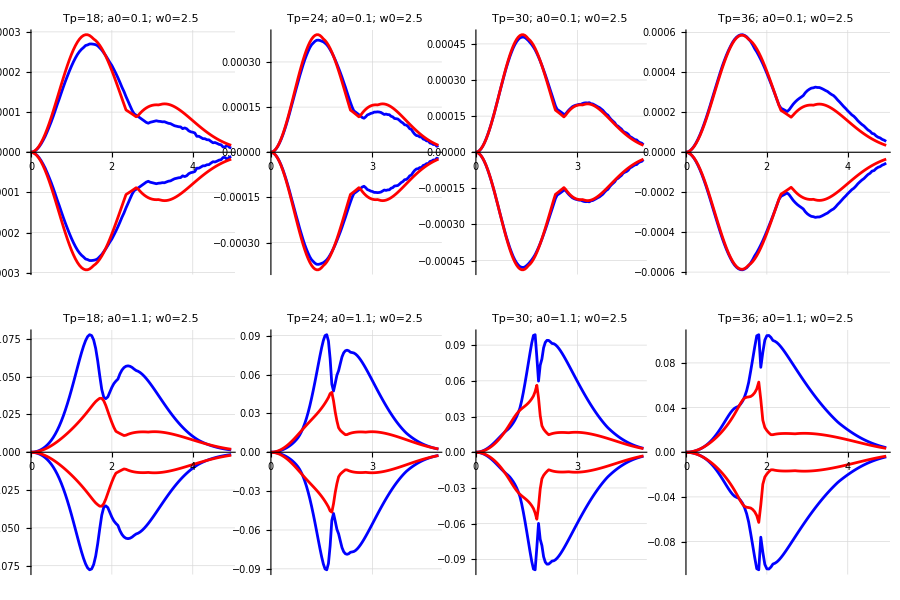

'Tp' act as an accuracy variable -> The more oscillation the more numerical errors are smoothed/averaged
It act the same as 'dx' with Smilei

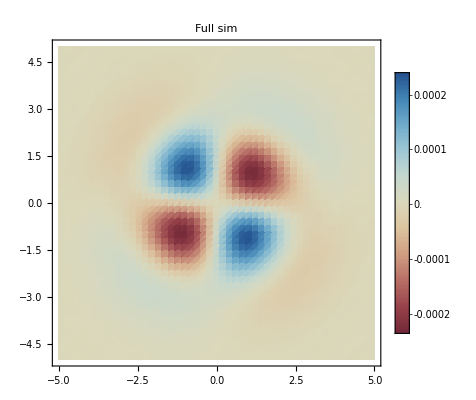

```mathematica
DensityPlot[MzDistrib[x0*l0,y0*l0,z0,0.1,w0,Tp,dt,50*l0,-1],
{y0,-2*w0/l0,2*w0/l0},{x0,-2*w0/l0,2*w0/l0},PlotPoints->{50,50},PlotLegends->Automatic,ColorFunction->"RedBlueTones",PlotRange->All,PlotLabel->"Full sim"]
```

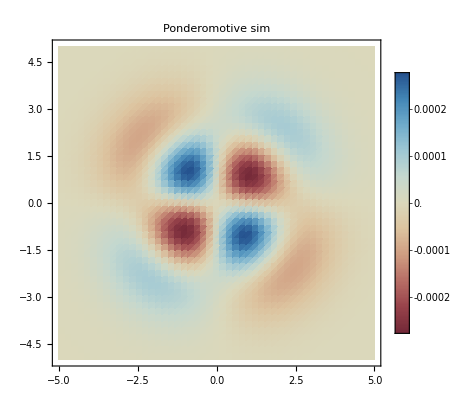

```mathematica
DensityPlot[MzDistribPondero[x0*l0,y0*l0,z0,0.1,w0,Tp,dt,tmax,-1],
{y0,-2*w0/l0,2*w0/l0},{x0,-2*w0/l0,2*w0/l0},PlotPoints->{50,50},PlotLegends->Automatic,ColorFunction->"RedBlueTones",PlotRange->All,PlotLabel->"Ponderomotive sim"]
```